# L0 Dipole Modeling

```mathematica
root=NotebookDirectory[]
```

/Users/cem52/accuser/erl/CERL/lattice_devel/CornellBNL/model/in/merge_3D/merge_dipole/

```mathematica
rawFilename="L0_LD.dat";
```

```mathematica
outputFilename = "L0_dipole_grid.bmad";
```

```mathematica
description="L0 dipole 3D field map"
```

L0 dipole 3D field map

## Options

```mathematica
myplotoptions={BaseStyle->{FontSize->15}, Frame->True};
SetOptions[Plot,myplotoptions];
SetOptions[ListPlot,myplotoptions];
SetOptions[ListLogPlot,myplotoptions];
SetOptions[ListVectorPlot,myplotoptions];
SetOptions[ListDensityPlot,myplotoptions];
```

## raw grid data

```mathematica
rawgriddat=Import[root<>rawFilename, "Table"];
```

```mathematica
rawgriddat[[1;;8]]//Grid
```

x | y | z | Bx | By | Bz
-0.02 | -0.01 | -0.3 | 1.079×10^-6 | -0.0002691 | 9.549×10^-6
-0.02 | -0.01 | -0.298 | 6.964×10^-7 | -0.0002717 | 0.00001209
-0.02 | -0.01 | -0.296 | 5.911×10^-7 | -0.0002749 | 0.00001443
-0.02 | -0.01 | -0.294 | 1.227×10^-6 | -0.0002796 | 0.00001477
-0.02 | -0.01 | -0.292 | 1.506×10^-6 | -0.0002828 | 0.00001591
-0.02 | -0.01 | -0.29 | 1.456×10^-6 | -0.0002846 | 0.00001723
-0.02 | -0.01 | -0.288 | 1.82×10^-6 | -0.0002881 | 0.00001558

```mathematica
xC=1;
yC=2;
zC=3;
BxC=4;
ByC=5;
BzC=6;
griddat=rawgriddat[[2;;-2]];
```

```mathematica
griddat0=Select[griddat,(#[[yC]]==0)&];
```

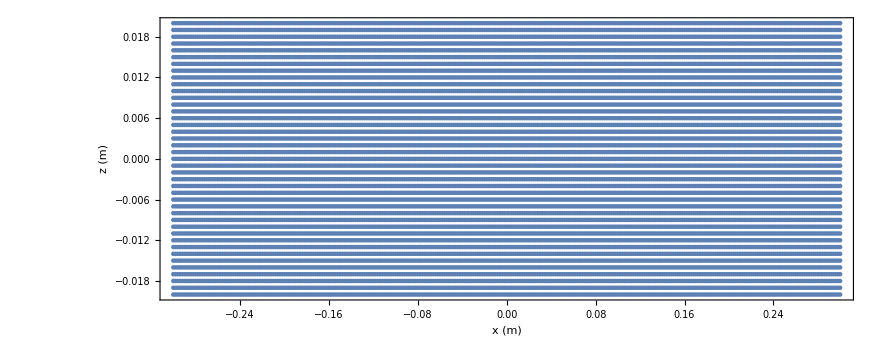

```mathematica
ListPlot[{#⟦zC ⟧, #⟦xC ⟧}&/@griddat0, FrameLabel->{"x (m)", "z (m)"}, AspectRatio->Automatic, ImageSize->600]
```

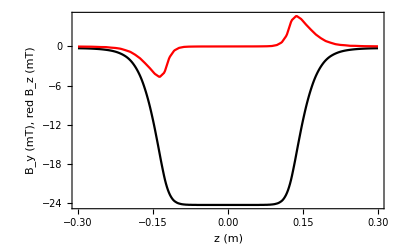

```mathematica
dat0=Select[griddat, (#[[xC]]==0)&&(#[[yC]]==0)&];
dat1=Select[griddat, (#[[xC]]==0)&&(#[[yC]]==0.01)&];
ListPlot[{{ #⟦zC ⟧, 10^3#⟦ByC⟧}&/@dat0,{ #⟦zC ⟧, 10^3#⟦BzC⟧}&/@dat1}, Joined->True, FrameLabel->{"z (m)", "B_y (mT), red B_z (mT) "},PlotRange->All, PlotStyle->{Black,Red}]
```

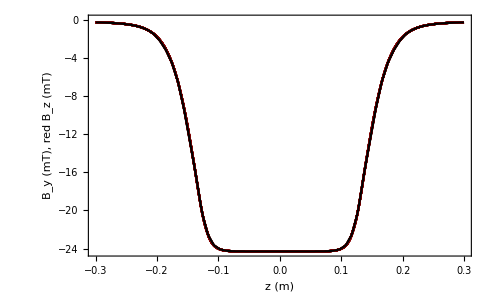

```mathematica
ListPlot[Table[{ #⟦zC ⟧, 10^3#⟦ByC⟧}&/@Select[griddat0, #⟦xC⟧==x&],{x,xlist}], Joined->True, FrameLabel->{"z (m)", "B_y (mT), red B_z (mT) "},PlotRange->All, PlotStyle->{Black,Red}]
```

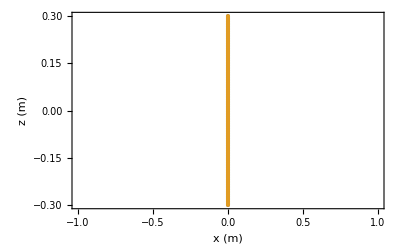

```mathematica
ListPlot[{{#⟦xC ⟧, #⟦zC ⟧}&/@dat0, {#⟦xC ⟧, #⟦zC ⟧}&/@dat1}, FrameLabel->{"x (m)", "z (m)"}]
```

```mathematica
{Min[dat0[[All,xC]]], Max[dat0[[All,xC]]], Min[dat1[[All,xC]]], Max[dat1[[All,xC]]]}
```

{0.,0.,0.,0.}

```mathematica
{Min[dat0[[All,zC]]], Max[dat0[[All,zC]]]}
```

{-0.3,0.3}

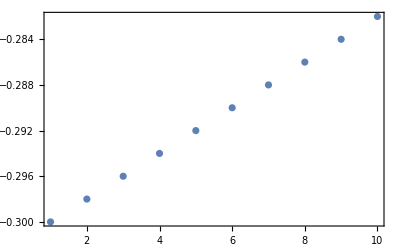

```mathematica
ListPlot[dat0[[1;;10,zC]],PlotRange->All]
```

## Verify Grid

```mathematica
refdat=griddat;
```

```mathematica
xlist=Sort[#[[xC]]&/@refdat, #1<#2&];xlist=Intersection[xlist,xlist];
ylist=Sort[#[[yC]]&/@refdat, #1<#2&];ylist=Intersection[ylist,ylist];
zlist=Sort[#[[zC]]&/@refdat, #1<#2&];zlist=Intersection[zlist,zlist];
xmax = Max[xlist];xmin = Min[xlist];xsize=xmax-xmin;
ymax = Max[ylist];ymin = Min[ylist];ysize=ymax-ymin;
zmax = Max[zlist];zmin = Min[zlist];zsize=zmax-zmin;
```

```mathematica
Grid[{{,"min (m)","max (m)"},{"x: ",xmin,xmax}, {"y: ",ymin,ymax},{"z: ",zmin,zmax}}, Frame->True, Alignment->Left]
```

| min (m) | max (m)
x:  | -0.02 | 0.02
y:  | -0.01 | 0.01
z:  | -0.3 | 0.3

```mathematica
spacings[mylist_]:=Part[Union[#,#]&/@{Table[mylist⟦i+1⟧-mylist⟦i⟧, {i,1,Length[mylist]-1}]},1];
spacings/@{xlist,ylist,zlist}
```

{{0.001,0.001,0.001,0.001},{0.001,0.001,0.001},{0.002,0.002,0.002,0.002,0.002,0.002,0.002}}

```mathematica
Δx = 0.001;
Δy = 0.001;
Δz = 0.002;

ixof[x_]:=Round[(x -xmin)/Δx];
iyof[y_]:=Round[(y -ymin)/Δy];
izof[z_]:=Round[(z -zmin)/Δz];

xof[ix_]:=xmin + ix Δx;
yof[iy_]:=ymin + iy Δy;
zof[iz_]:=zmin + iz Δz;
```

```mathematica
izof[zmin]
```

0

```mathematica
ixof[xmin]
```

0

```mathematica
ListPlot[{izof[#[[zC]]],ixof[#[[xC]]]}&/@refdat, AspectRatio->Automatic]
```

-Graphics-

```mathematica
ixof[0]
```

20

```mathematica
iyof[0]
```

10

```mathematica
izof[0]
```

150

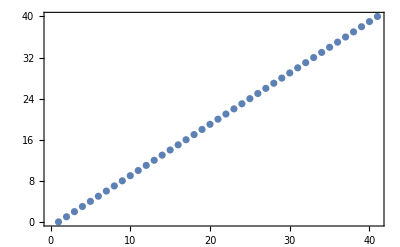

```mathematica
ListPlot[ixof/@xlist]
```

## Make Bmad Grid

```mathematica
fieldmapdir = root;
```

```mathematica
fieldscale = 1/Max[Abs[dat0⟦All, ByC⟧]]
```

41.1523

```mathematica
(*pt format: pt(ir, iz) = ( (ErRe,ErIm), (0,0), (EzRe,EzIm), (0,0), (BrRe,BrIm), (0,0), (BϕRe, BϕIm) , (0,0) ) *)
MakeBmadGrid[dat_]:=Module[{header, body, ptlist},
header = {"{ ", "!"<>description, "! Scaled for maximum on-axis By = 1 T"};
body = {
{"type = xyz,"},
{"r0 = (",xmin,"," ,ymin ,"," ,0 ,")," },
{"dr = (", Δx,",", Δy, ",", Δz,"),"}
};

ptlist ={
"pt(", ixof[ #⟦xC⟧  ], "," ,iyof[#⟦yC⟧],"," ,izof[#⟦zC⟧] ,") = (0,0,0,",
	fieldscale*#⟦BxC⟧,",",fieldscale*#⟦ByC⟧,",",fieldscale*#⟦BzC⟧, ")",","}&/@dat;
ptlist[[-1,-1]] = "}";
Join[header,body,  ptlist]

]
```

```mathematica
griddata=MakeBmadGrid[refdat ];
```

```mathematica
Export[fieldmapdir <>outputFilename  ,griddata, "Table", "FieldSeparators"->""];
```

## Integrate

Widen map:

```mathematica
griddat0extended1=(Flatten[{#⟦1⟧ + 0.04 + Δx, #⟦2;;⟧}]&/@griddat0);
griddat0extended2=(Flatten[{#⟦1⟧ -( 0.04 + Δx), #⟦2;;⟧}]&/@griddat0);
```

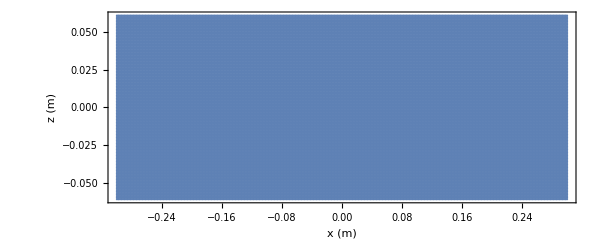

```mathematica
mygriddat0= Join[griddat0,griddat0extended1, griddat0extended2];

ListPlot[{#⟦zC ⟧, #⟦xC ⟧}&/@mygriddat0, FrameLabel->{"x (m)", "z (m)"}, AspectRatio->Automatic, ImageSize->600]
```

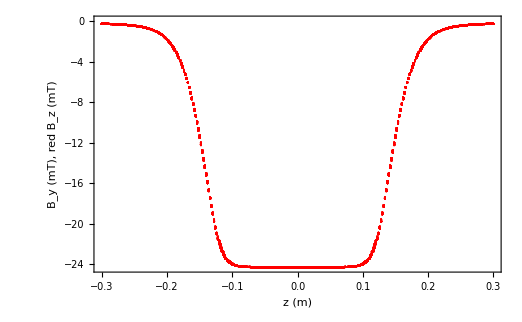

```mathematica
ListPlot[{ #⟦zC ⟧, 10^3#⟦ByC⟧}&/@mygriddat0, Joined->False, FrameLabel->{"z (m)", "B_y (mT), red B_z (mT) "},PlotRange->All, PlotStyle->{Black,Red}]
```

```mathematica
griddat0⟦All, xC⟧//Max
```

0.02

```mathematica
factor =-0.7040564178427797*0.9902869541083827
```

-0.697218

```mathematica
zmax = 0.3;
```

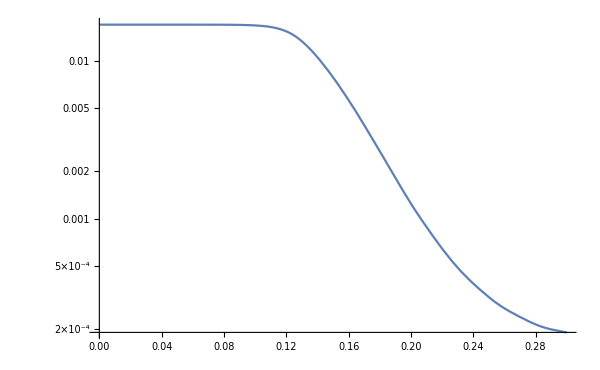

```mathematica
myBy= Interpolation[{{#[[zC]],#[[xC]]},factor #[[ByC]]}&/@(mygriddat0)];
LogPlot[myBy[z,0], {z,0,zmax}, FrameLabel->{"z (m)", "B_y (T)"}]
```

```mathematica
BL = -NIntegrate[myBy[z,0], {z,0,zmax}]
```

-0.00259203

```mathematica
(*Bmad*)
BmadBL = 2.05534 10^-2* .25400;BmadBL /2
```

0.00261028

```mathematica
en = 6 10^6;
By = .;
mc2 = 0.511 10^6;
cpz0 = Sqrt[en^2-mc2^2];
c = 299792458.;
q = -1;

ctmax = 0.3;
Clear[sol];
MySol[x0_]:=NDSolve[{
x'[ct] == cpx[ct]/en,
cpx'[ct] == -q c  cpz[ct]/en myBy[z[ct], x[ct]],
z'[ct] == cpz[ct]/en,
cpz'[ct] == q c cpx[ct]/en myBy[z[ct], x[ct]],
 x[0]==x0, cpx[0]==0, z[0]==0, cpz[0] == cpz0},{x,cpx, z, cpz},{ct,ctmax }];
sol =MySol[0]⟦1⟧
```

{x→InterpolatingFunction[{{0., 0.3}}, <>],cpx→InterpolatingFunction[{{0., 0.3}}, <>],z→InterpolatingFunction[{{0., 0.3}}, <>],cpz→InterpolatingFunction[{{0., 0.3}}, <>]}

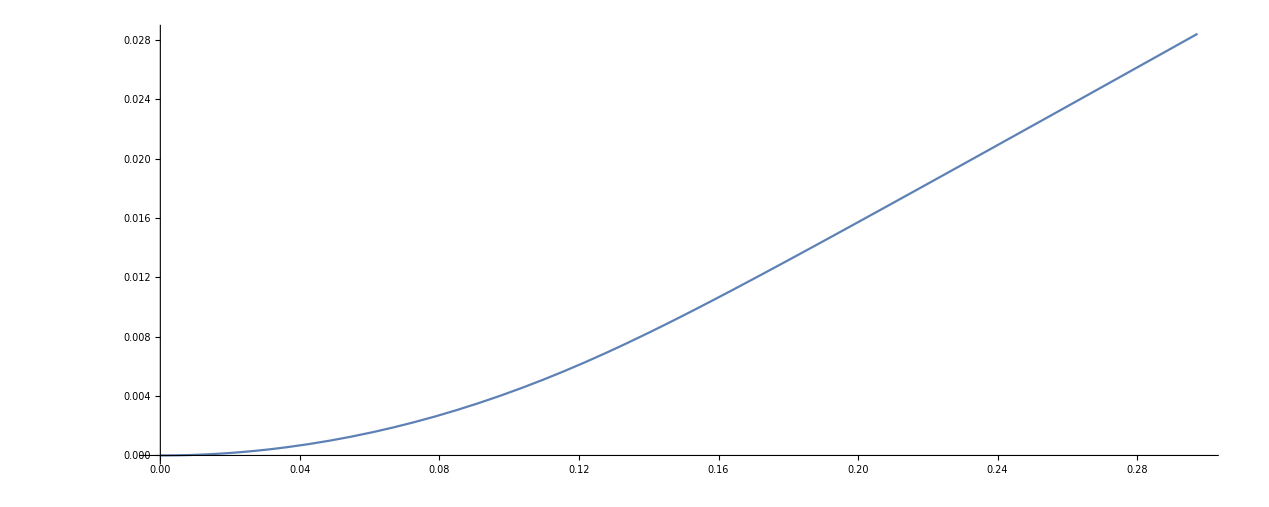

```mathematica
ParametricPlot[{z[ct], x[ct]}/.sol, {ct,0,ctmax}, AspectRatio->Automatic]
```

```mathematica
xlist = Table[x, {x,-.01, .01, .001}]
```

{-0.01,-0.009,-0.008,-0.007,-0.006,-0.005,-0.004,-0.003,-0.002,-0.001,0.,0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01}

```mathematica
MyAngleAt[x0_]:=Module[{}, Quiet[180/π ArcTan[cpz[ctmax], cpx[ctmax]]/.MySol[x0]⟦1⟧]];
this = MyAngleAt[0];
target = -15/2;
factor = target/this
```

-1.00321

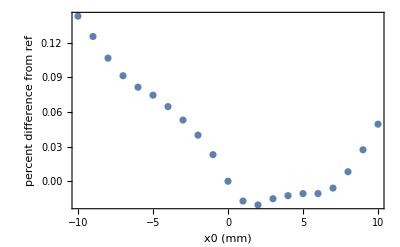

```mathematica
refangle = MyAngleAt[0];
ListPlot[Transpose[{1000 xlist,(1-( MyAngleAt/@xlist)/refangle ) 100}], FrameLabel->{"x0 (mm)", "percent difference from ref"}]
```

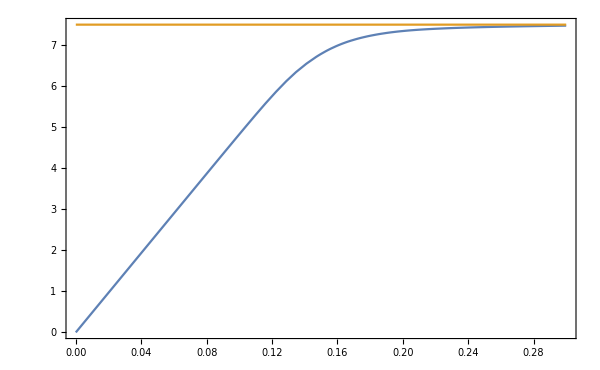

```mathematica
Plot[{ 180/π ArcTan[cpz[ct], cpx[ct]]/.sol, 7.5},  {ct,0,ctmax}]
```

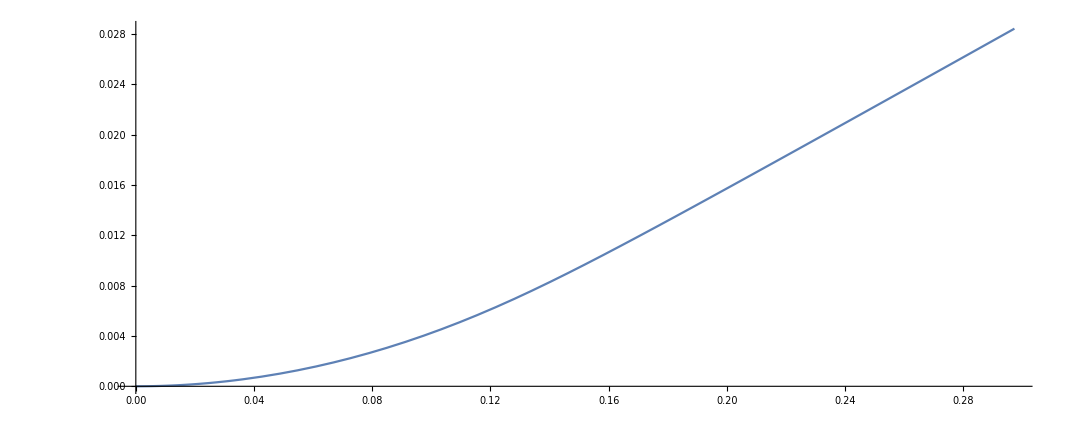

```mathematica
myplot[x0_]:=Module[{ss},Quiet[ ss=MySol[x0]⟦1⟧];ParametricPlot[ {z[ct], x[ct]}/.ss, {ct,0,ctmax}]];
myplot[0]
```

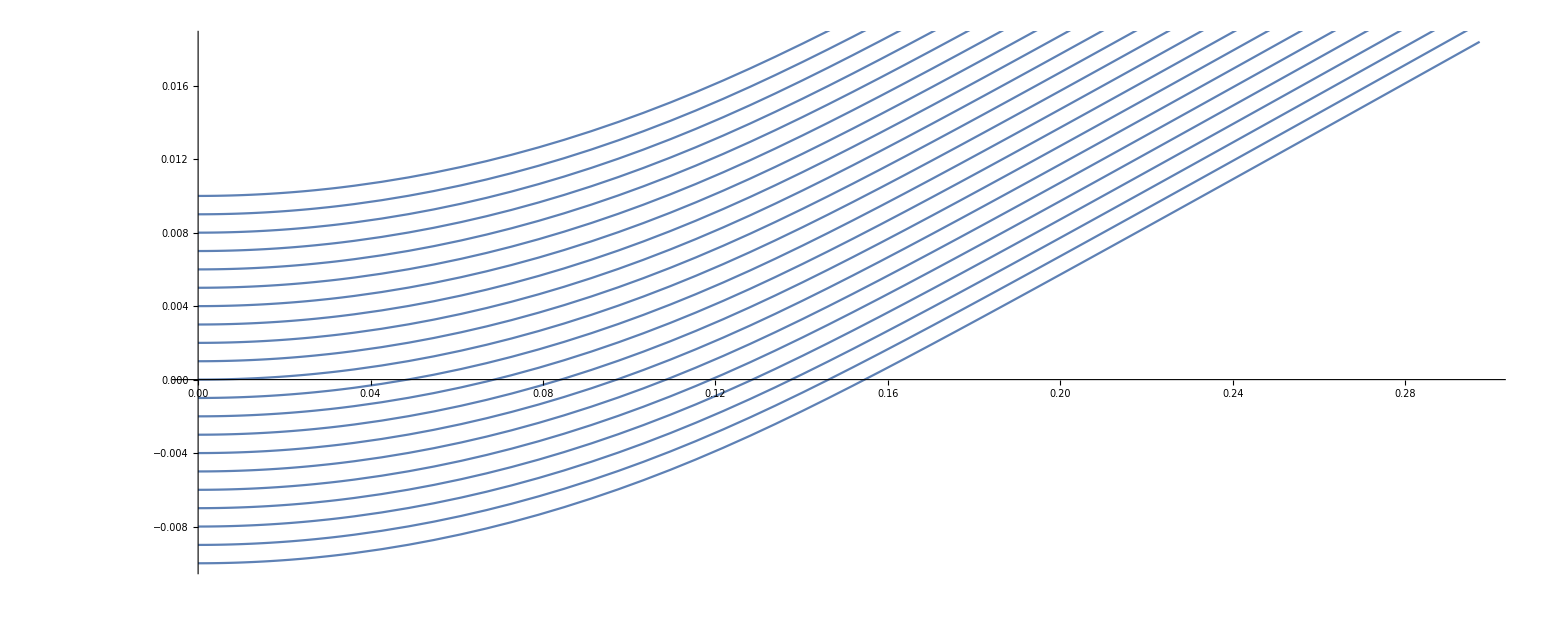

```mathematica
Show[myplot/@xlist]
```

## Arc Geometry

```mathematica
θdesign = 15 π/180. /2;
Ldesign = 10 0.0254/2;
ρ = Ldesign/θdesign;
Ldesign /ρ* 180/π
```

7.5

```mathematica
Clear[DesignGeometry];
DesignGeometry[s_, Lbend_:Ldesign]:= Module[{ρ = Lbend/θdesign},
Piecewise[{
{{ρ Sin[s/ρ], ρ(1-Cos[s/ρ])}, s<Lbend}, 
{{ρ Sin[θdesign ], ρ(1-Cos[θdesign ])} + (s - Lbend) {Cos[θdesign], Sin[θdesign]} , s ≥  Lbend}
}]

];
2 ArcTan@@DesignGeometry[Ldesign] 180/π
```

7.5

```mathematica
mrot = RotationMatrix[-θdesign]
```

{{0.991445,0.130526},{-0.130526,0.991445}}

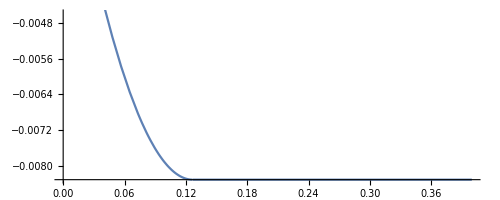

```mathematica
ParametricPlot[mrot.DesignGeometry[s], {s,0,.4}]
```

```mathematica
Ldesign
```

0.127

```mathematica
0.16 2 / 0.0254
```

12.5984

```mathematica
colwyndat = Import[NotebookDirectory[]<>"colwyn_jorb.txt", "Table"];
ListPlot[colwyndat]
```

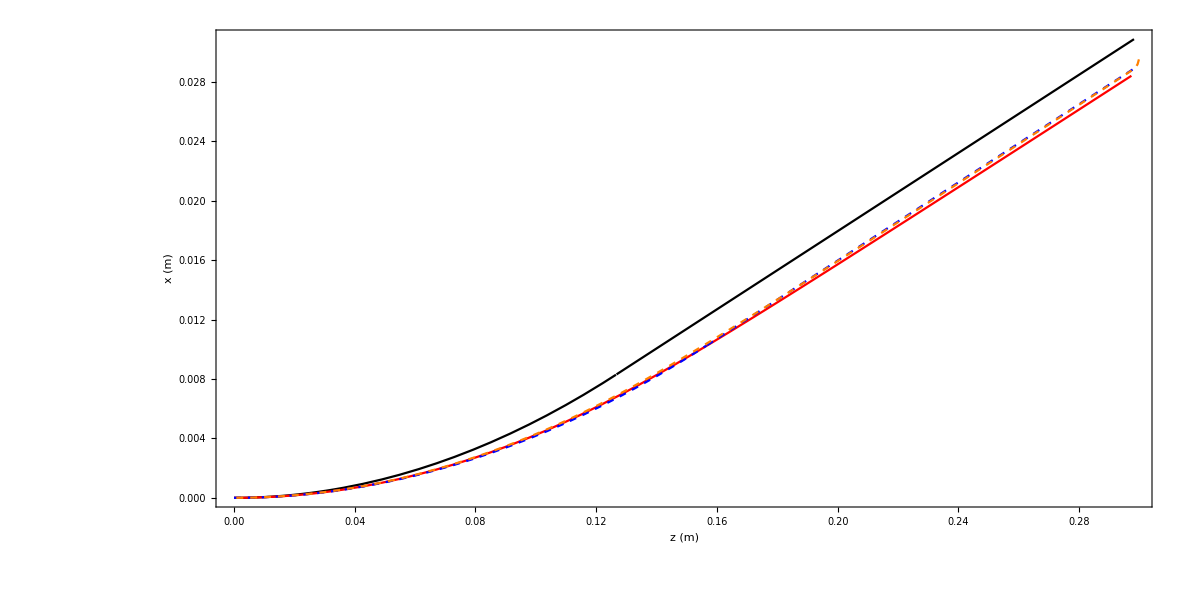

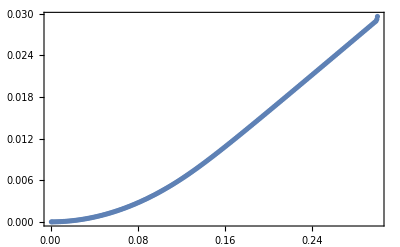

```mathematica
smax = 0.3;
Show[
ParametricPlot[
DesignGeometry[s, Ldesign], {s,0,smax}, Frame->True,PlotStyle->Black, FrameLabel->{"z (m)", "x (m)"}, BaseStyle->{FontSize->15}],
ParametricPlot[{z[ct], x[ct]}/.sol, {ct,0,ctmax}, AspectRatio->1, PlotStyle->Red],
ParametricPlot[
DesignGeometry[s, 1.20*15/2 π/180], {s,0,smax}, Frame->True,PlotStyle->{Dashed, Blue}, FrameLabel->{"z (m)", "x (m)"}, BaseStyle->{FontSize->15}],
ListPlot[colwyndat, PlotStyle->{Dashed, Orange}, Joined->True],
ImageSize->1200, AspectRatio->1/2

]
```

```mathematica
0.254 - 1.25*15 π/180
```

```mathematica
-0.0732492347489368 * 1.5
```

-0.109874

```mathematica
0.8-0.019748/2
```

0.790126

```mathematica
0.163 * 2 / 0.0254
```

12.8346

```mathematica
(0.163 * 2)/□
```

1.24523

```mathematica
ArcTan@@({cpz[0.3], cpx[0.3]}/.sol) 180/π
```

7.49993

```mathematica
ArcTan@@DesignGeometry[Ldesign, Ldesign] 180/π
```

3.75

ReplaceAll::reps: {2.59184×10^-6} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {0.00259443} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {0.00518627} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

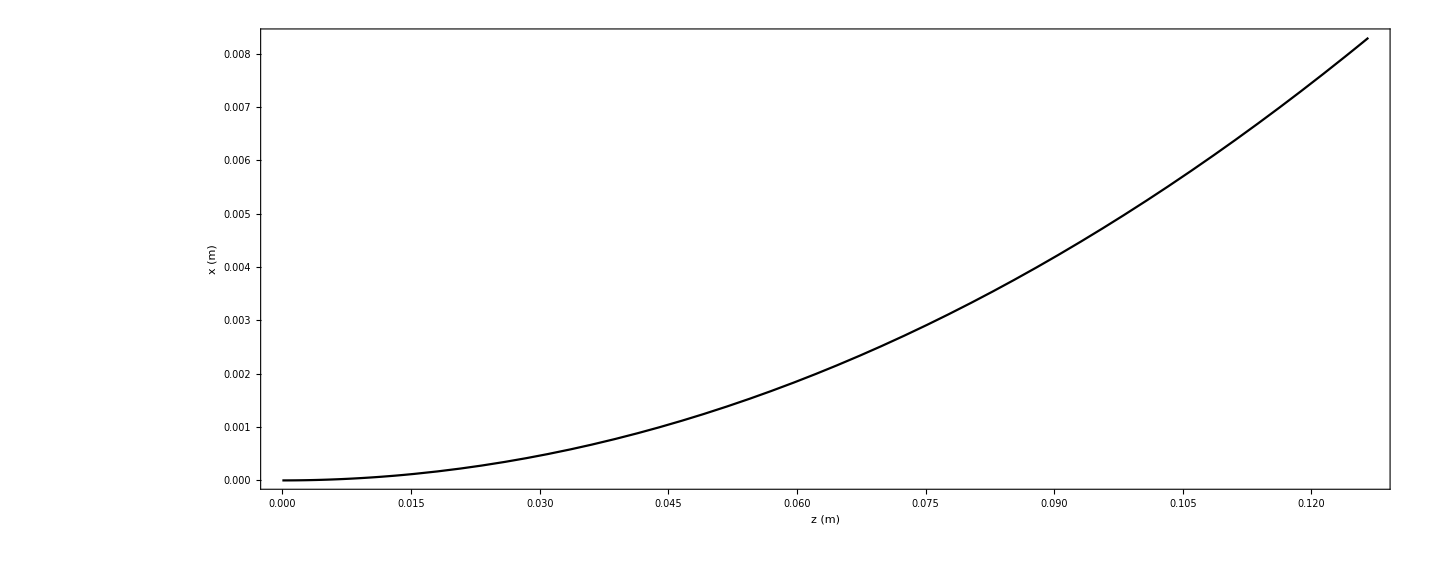

```mathematica
ParametricPlot[
{
DesignGeometry[s, Ldesign],
({z[s], x[s]}/.s)},
 {s,0,Ldesign}, Frame->True,PlotStyle->{Black, Red}, FrameLabel->{"z (m)", "x (m)"}, BaseStyle->{FontSize->15}]
```